```mathematica
Clear["Global`*"];On[Assert];
```

# 非线性方程求根

申奥 2017012518 计科70

本实验的主要目的在于实现牛顿法解非线性方程的一个实现。同时比较改进后的算法与之前算法使用的结果来比较两种算法收敛速度的快慢。

## 牛顿法的实现与比较

### 牛顿法的实现

实现显然。只需一行。

```mathematica
newtonSolveNR[f_,xi_]:=Block[{s,x=N@xi,BracketingBar=Abs},NestWhileList[#-f[#]/f'[#]&,x,|#1-#2|≥ϵ&,2]]
```

### 阻尼牛顿法的实现

阻尼牛顿法的实现思路与牛顿法近似，但是我们需要不断更新因子 λ 的值来保证函数的绝对值减小。因此我们需要一个函数来更新并保存 λ 的值。同时，为了方便追踪算法的运行路径，我们需要保存每一步最后的 λ 和相应的迭代解，这可以用 Sow[] 函数来实现。最后，这样得到的结果是一个复杂的列表，我们需要将列表格式化成更容易阅读的形式。

首先我们考虑需要的两个常数：一个是下降因子λ，另外一个是判停阈值ϵ。

```mathematica
λ[0]=1;
ϵ=0.000001;
```

同时利用逐次减半法来更新λ。

```mathematica
λ[i_]:=λ[i](*对λ使用缓存*)=λ[i-1]/2.
λ/:Subscript[λ,x_Integer]:=λ[x](*利用下标访问λ*)
```

主循环，与牛顿法的区别在于里面增加了一个内循环来利用阻尼因子 λ 保证函数绝对值必定减小。

```mathematica
newtonSolve[f_,xi_]:=Block[{k=0,s,xn=Infinity,xo=N[xi],i,BracketingBar=Abs},
Reap[
While[|f[xo]|>ϵ,
s=f[xo]/f'[xo];
xn=xo-s;
i=0;
While[|f[xn]|≥|f[xo]|,
xn=xo-Subscript[λ, i] s;
i++;
];
k++;
Sow[{Subscript[λ, i],xn}];(*保存每次迭代歩最后的解和λ值*)
xo=xn;
];xo]
]
```

辅助函数，用来将最后输出的 λ 值等过程信息转化为表格

```mathematica
newtonPrettyPrint=Apply[Curry[TableForm][TableHeadings->{Automatic,{"最终 λ","迭代解"}}],#,{1}]&;
newtonNRPrettyPrint=MapAt[Curry[TableForm][TableHeadings->{Automatic,{"迭代解"}}],{Last@#,List/@#},2]&;
```

### 实际验证

使用两种方法和内置等数值求解工具分别试解 x^3-x-1=0 得

```mathematica
newtonSolve[#^3-#-1&,0.6]//newtonPrettyPrint
```

{1.32472, | 最终 λ | 迭代解
1 | 0.015625 | 1.14062
2 | 1 | 1.36681
3 | 1 | 1.32628
4 | 1 | 1.32472
5 | 1 | 1.32472}

```mathematica
newtonSolveNR[#^3-#-1&,0.6]//newtonNRPrettyPrint
```

{1.32472, | 迭代解
1 | 0.6
2 | 17.9
3 | 11.9468
4 | 7.98552
5 | 5.35691
6 | 3.625
7 | 2.50559
8 | 1.82013
9 | 1.46104
10 | 1.33932
11 | 1.32491
12 | 1.32472
13 | 1.32472}

```mathematica
FindRoot[x^3-x-1==0,{x,0.6}]
```

{x→1.32472}

内建方法验证了我们的实现是正确的。同时，可以看到牛顿法需要迭代12步结果收敛，而采用阻尼技术之后只需4步迭代即可收敛。
对于另外一个方程，我们的观察仍然也是正确的：

```mathematica
newtonSolve[-#^3+5#&,1.35]//newtonPrettyPrint
```

{2.23607, | 最终 λ | 迭代解
1 | 0.0625 | 2.49696
2 | 1 | 2.27198
3 | 1 | 2.2369
4 | 1 | 2.23607
5 | 1 | 2.23607}

```mathematica
newtonSolveNR[-#^3+5#&,1.35]//newtonNRPrettyPrint
```

{2.23607, | 迭代解
1 | 1.35
2 | 10.5257
3 | 7.12429
4 | 4.91078
5 | 3.51691
6 | 2.70974
7 | 2.33694
8 | 2.24224
9 | 2.23609
10 | 2.23607
11 | 2.23607}

```mathematica
FindRoot[-x^3+5x==0,{x,1.35}]
```

{x→2.23607}

可以看到，由于阻尼的应用保证了迭代法的每一步 f(x) 的绝对值都会下降，因此可以在不增大很多计算量的前提下起到减少迭代步数，加速收敛的作用。

## 用 fzerox 算法求贝塞尔函数零点

贝塞尔函数 0x 如下图所示，在实验中我们需要实现书上给出的二次差值求根算法 fzerox 求出贝塞尔函数的前十个非负零点，并与精确值相比较。

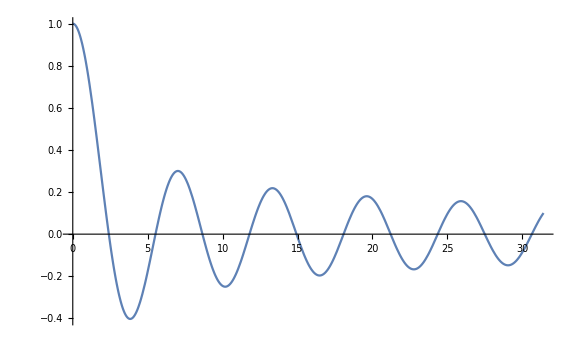

```mathematica
besselPlot=Plot[BesselJ[0,x],{x,0,10 Pi},ImageSize->Large]
```

为便利计，首先打印出贝塞尔函数的前十个正零点如下：

```mathematica
Table[BesselJZero[0,i],{i,1,10}]//N
```

{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711,21.2116,24.3525,27.4935,30.6346}

### fzerox 算法的实现

根据课本 matlab 代码容易得到如下实现。

```mathematica
fzerox[f_,aa_Real,bb_Real,vars___]:=
Block[{a,b,c,fa,fb,fc,d,e,tol,p,q,r,s,mid},
a=aa;
b=bb;
fa=f[a,vars];
fb=f[b,vars];
Assert[Sign[fa]≠Sign[fb]];
c=a;
fc=fa;
d=b-c;
e=d;
While[Abs[fb]>ϵ,
If[Sign[fa]==Sign[fb],
a=c;fa=fc;
d=b-c;e=d;
];
If[Abs[fa]<Abs[fb],
c=a;a=b;b=c;
fc=fa;fa=fb;fb=fc;
];
mid=0.5(a-b);
tol=2 ($MachineEpsilon) Max[Abs@b,1];
If[(Abs[mid]<tol)∨(fb==0),
Break[]];
If[(Abs[e]<tol)∨(Abs[fc]≤Abs[fb]),
d=mid;e=mid;
,
s=fb/fc;
If[a==c,
p=2 mid s;
q=1-s;
,
q=fc/fa;
r=fb/fa;
p=s (2 mid q (q-r) -(b-c)(r-1));
q=(q-1)(r-1)(s-1);
];
If[p>0,q=-q,p=-p];
If[(2 p < (3 mid q -Abs[tol q]) )∧(p<Abs[0.5 e q]),
e=d;d=p/q;
,
d=mid;e=mid;
];
];
c=b;fc=fb;
If[Abs@d>tol,b=b+d;,b=b-Sign[b-a] tol;];
fb=f[b,vars];
];
Return[b]]
```

根据之前给出的函数图像，我们可以大概给出零点可能存在的区间，然后根据这些区间来运行算法寻找确切的零点值。

```mathematica
besselZeros=Table[fzerox[BesselJ[0,#]&,i,i+3.0],{i,{2.,5.,8.,11.,14.,18.,21.,24.,27.,30.}}]
```

{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711,21.2116,24.3525,27.4935,30.6346}

将所得零点值与函数图像相比较，可以看出所求的正确性。

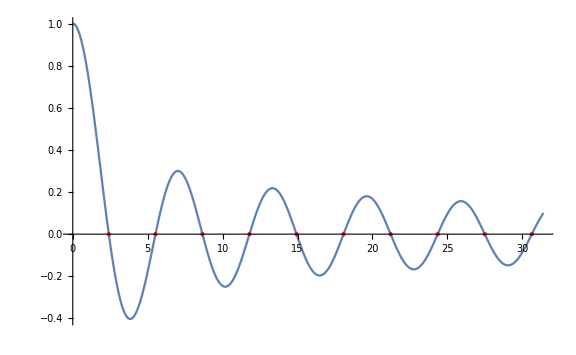

```mathematica
Show[besselPlot,Graphics[{PointSize[Large],Red,Point[{#,0.0}&/@besselZeros]}]]
```

#### 实验总结

可以看到，这种结合多种求根方式的算法确实可以比较快的求出较复杂函数的零点值，且不需要计算函数的导数。但是此法实现比较繁琐。